```mathematica
Clear["`*"];
```

```mathematica
list=Import["https://gist.githubusercontent.com/bczhc/3c650a68ae85d026385037e721078a9b/raw/eee00d466afa3ea8805251f4139fd8a076e3ff9d/a.csv","CSV","Numeric"->False]⟦2;;⟧;
```

```mathematica
intItpr=Read[StringToStream@#,Number]&;
```

```mathematica
toDateTime[str_String]:=DateObject[intItpr/@StringSplit[str,{"-"," ", ":"}]];
```

```mathematica
items={toDateTime[#⟦5⟧],#⟦2⟧}&/@list;
```

```mathematica
resolveDNF[str_String]:=StringSplit[str,{"DNF(",")"}]⟦1⟧;
```

```mathematica
dnfItems={#⟦1⟧,intItpr@resolveDNF@#⟦2⟧}&/@Select[items,StringContainsQ[#⟦2⟧,"DNF"]&];
solvedItems={#⟦1⟧,intItpr@#⟦2⟧}&/@Select[items,!StringContainsQ[#⟦2⟧,"DNF"]&];
```

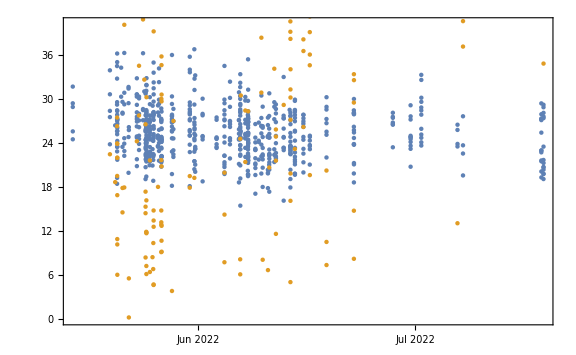

```mathematica
DateListPlot[{solvedItems,dnfItems},ImageSize->Large,Joined->False,DateTicksFormat->{"Day"," ", "MonthNameShort"," ","Year"},FrameTicks->Automatic]
```